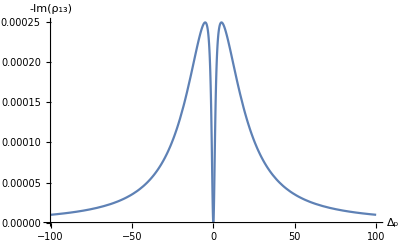

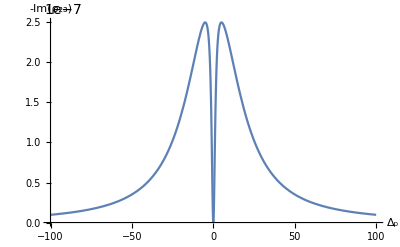

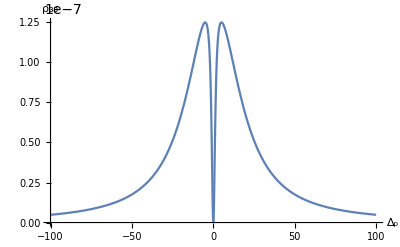

```mathematica
Subscript[Γ, 31]=20;Subscript[Γ, 32]=20;Subscript[Δ, 2]=0;
Subscript[Ω, p] =0.01;
Subscript[Ω, c]=10;
Subscript[γ, 3 deph]=0;
Subscript[γ, 2 deph]=0;
ℏ=1;
Subscript[Γ, 12]=0;
H=-ℏ/2*{{0,0,Subscript[Ω, p]*Exp[-ⅈ*a*t]},{0,0,Subscript[Ω, c]*Exp[-ⅈ*Subscript[Δ, 2]*t]},{Subscript[Ω, p]*Exp[ⅈ*a*t],Subscript[Ω, c]*Exp[ⅈ*Subscript[Δ, 2]*t],0}};densitymatrix={{Subscript[ρ, 11],Subscript[ρ, 12],Subscript[ρ, 13]},{Subscript[ρ, 21],Subscript[ρ, 22],Subscript[ρ, 23]},{Subscript[ρ, 31],Subscript[ρ, 32],Subscript[ρ, 33]}};U={{1,0,0},{0,Exp[ⅈ*(a-Subscript[Δ, 2])*t],0},{0,0,Exp[ⅈ*a*t]}};NewH=Simplify[Conjugate[U].H.U-ⅈ*Conjugate[U].D[U,t],Element[t,Reals]&&Element[a,Reals]&&Element[Subscript[Δ, 2],Reals]];sigma13={{0,0,1},{0,0,0},{0,0,0}};sigma31={{0,0,0},{0,0,0},{1,0,0}};sigma33={{0,0,0},{0,0,0},{0,0,1}};sigma23={{0,0,0},{0,0,1},{0,0,0}};sigma32={{0,0,0},{0,0,0},{0,1,0}};sigma22={{0,0,0},{0,1,0},{0,0,0}};sigma12={{0,1,0},{0,0,0},{0,0,0}};sigma21={{0,0,0},{1,0,0},{0,0,0}};sigma11={{1,0,0},{0,0,0},{0,0,0}};L=Subscript[Γ, 31]/2*(2*sigma13.densitymatrix.sigma31-sigma33.densitymatrix-densitymatrix.sigma33)+Subscript[Γ, 32]/2*(2*sigma23.densitymatrix.sigma32-sigma33.densitymatrix-densitymatrix.sigma33)+Subscript[γ, 2deph]/2*(2*sigma22.densitymatrix.sigma22-sigma22.densitymatrix-densitymatrix.sigma22)+Subscript[γ, 3deph]/2*(2*sigma33.densitymatrix.sigma33-sigma33.densitymatrix-densitymatrix.sigma33)+Subscript[Γ, 12]/2*(2*sigma12.densitymatrix.sigma21-sigma22.densitymatrix-densitymatrix.sigma22)+Subscript[Γ, 12]/2*(2*sigma21.densitymatrix.sigma12-sigma11.densitymatrix-densitymatrix.sigma11);M=Simplify[-ⅈ*(NewH.densitymatrix-densitymatrix.NewH)+L,Element[t,Reals]&&Element[a,Reals]&&Element[Subscript[Δ, 2],Reals]];M[[3,3]]=Subscript[ρ, 11]+Subscript[ρ, 22]+Subscript[ρ, 33]-1;
Aa={};
B1={};
C1={};
F1[a_]:=-Im[Subscript[ρ, 13]/.Solve[{M[[1,1]]==0,M[[1,2]]==0,M[[1,3]]==0,M[[2,1]]==0,M[[2,2]]==0,M[[2,3]]==0,M[[3,1]]==0,M[[3,2]]==0,M[[3,3]]==0},{Subscript[ρ, 11],Subscript[ρ, 12],Subscript[ρ, 13],Subscript[ρ, 21],Subscript[ρ, 22],Subscript[ρ, 23],Subscript[ρ, 31],Subscript[ρ, 32],Subscript[ρ, 33]}]][[1]];
F2[a_]:=-Im[Subscript[ρ, 23]/.Solve[{M[[1,1]]==0,M[[1,2]]==0,M[[1,3]]==0,M[[2,1]]==0,M[[2,2]]==0,M[[2,3]]==0,M[[3,1]]==0,M[[3,2]]==0,M[[3,3]]==0},{Subscript[ρ, 11],Subscript[ρ, 12],Subscript[ρ, 13],Subscript[ρ, 21],Subscript[ρ, 22],Subscript[ρ, 23],Subscript[ρ, 31],Subscript[ρ, 32],Subscript[ρ, 33]}]][[1]];
F3[a_]:=Abs[Subscript[ρ, 33]/.Solve[{M[[1,1]]==0,M[[1,2]]==0,M[[1,3]]==0,M[[2,1]]==0,M[[2,2]]==0,M[[2,3]]==0,M[[3,1]]==0,M[[3,2]]==0,M[[3,3]]==0},{Subscript[ρ, 11],Subscript[ρ, 12],Subscript[ρ, 13],Subscript[ρ, 21],Subscript[ρ, 22],Subscript[ρ, 23],Subscript[ρ, 31],Subscript[ρ, 32],Subscript[ρ, 33]}]][[1]];
Plot[F1[a],{a,-100,100},PlotRange->All,AxesLabel->{Subscript[Δ, p],-Im[Subscript[ρ, 13]]}, AxesOrigin->{-100,0}]
Plot[F2[a],{a,-100,100},PlotRange->All,AxesLabel->{Subscript[Δ, p],-Im[Subscript[ρ, 23]]}, AxesOrigin->{-100,0}]
Plot[F3[a],{a,-100,100},PlotRange->All,AxesLabel->{Subscript[Δ, p],Subscript[ρ, 33]}, AxesOrigin->{-100,0}]
(*For[a=-500,a≤500,a=a+0.1,{Aa=Append[Aa,{Aa,F1[a]}],
B1=Append[B1,F2[a]],C1=Append[C1,F3[a]]}]Aa=Flatten[Aa];B1=Flatten[B1];C1=Flatten[C1];
ListPlot[Aa,PlotRange->{Min[0,Min[Aa]*1.05],Max[Aa]*1.05}]
ListPlot[B1,PlotRange->{Min[0,Min[B1]*1.05],Max[B1]*1.05}]
ListPlot[C1,PlotRange->{Min[0,Min[C1]*1.05],Max[C1]*1.05}]*)
```

```mathematica
H=-ℏ/2*{{0,0,Subscript[Ω, p]*Exp[-ⅈ*a*t]},{0,0,Subscript[Ω, c]*Exp[-ⅈ*Subscript[Δ, 2]*t]},{Subscript[Ω, p]*Exp[ⅈ*a*t],Subscript[Ω, c]*Exp[ⅈ*Subscript[Δ, 2]*t],0}};densitymatrix={{Subscript[ρ, 11],Subscript[ρ, 12],Subscript[ρ, 13]},{Subscript[ρ, 21],Subscript[ρ, 22],Subscript[ρ, 23]},{Subscript[ρ, 31],Subscript[ρ, 32],Subscript[ρ, 33]}};U={{1,0,0},{0,Exp[ⅈ*(a-Subscript[Δ, 2])*t],0},{0,0,Exp[ⅈ*a*t]}};NewH=Simplify[Conjugate[U].H.U-ⅈ*Conjugate[U].D[U,t],Element[t,Reals]&&Element[a,Reals]&&Element[Subscript[Δ, 2],Reals]];
```

```mathematica
NewH
```

{{0,0,-(ℏ Ω_p)/2},{0,a-Δ_2,-(ℏ Ω_c)/2},{-(ℏ Ω_p)/2,-(ℏ Ω_c)/2,a}}

```mathematica
Subscript[Δ, 2]=0;
Subscript[γ, 3 deph]=0;
Subscript[γ, 2 deph]=0;
ℏ=1;
Subscript[Γ, 12]=0;Subscript[Γ, 31]=Subscript[Γ, 32];
(*Subscript[Ω, p]=0.01 Subscript[Ω, c];*)
(*Subscript[Γ, 31]=0.001;Subscript[Γ, 32]=0.001;*)H=-ℏ/2*{{0,0,Subscript[Ω, p]*Exp[-ⅈ*a*t]},{0,0,Subscript[Ω, c]*Exp[-ⅈ*Subscript[Δ, 2]*t]},{Subscript[Ω, p]*Exp[ⅈ*a*t],Subscript[Ω, c]*Exp[ⅈ*Subscript[Δ, 2]*t],0}};densitymatrix={{Subscript[ρ, 11],Subscript[ρ, 12],Subscript[ρ, 13]},{Subscript[ρ, 21],Subscript[ρ, 22],Subscript[ρ, 23]},{Subscript[ρ, 31],Subscript[ρ, 32],Subscript[ρ, 33]}};U={{1,0,0},{0,Exp[ⅈ*(a-Subscript[Δ, 2])*t],0},{0,0,Exp[ⅈ*a*t]}};NewH=Simplify[Conjugate[U].H.U-ⅈ*Conjugate[U].D[U,t],Element[t,Reals]&&Element[a,Reals]&&Element[Subscript[Δ, 2],Reals]];sigma13={{0,0,1},{0,0,0},{0,0,0}};sigma31={{0,0,0},{0,0,0},{1,0,0}};sigma33={{0,0,0},{0,0,0},{0,0,1}};sigma23={{0,0,0},{0,0,1},{0,0,0}};sigma32={{0,0,0},{0,0,0},{0,1,0}};sigma22={{0,0,0},{0,1,0},{0,0,0}};sigma12={{0,1,0},{0,0,0},{0,0,0}};sigma21={{0,0,0},{1,0,0},{0,0,0}};sigma11={{1,0,0},{0,0,0},{0,0,0}};L=Subscript[Γ, 31]/2*(2*sigma13.densitymatrix.sigma31-sigma33.densitymatrix-densitymatrix.sigma33)+Subscript[Γ, 32]/2*(2*sigma23.densitymatrix.sigma32-sigma33.densitymatrix-densitymatrix.sigma33)+Subscript[γ, 2deph]/2*(2*sigma22.densitymatrix.sigma22-sigma22.densitymatrix-densitymatrix.sigma22)+Subscript[γ, 3deph]/2*(2*sigma33.densitymatrix.sigma33-sigma33.densitymatrix-densitymatrix.sigma33)+Subscript[Γ, 12]/2*(2*sigma12.densitymatrix.sigma21-sigma22.densitymatrix-densitymatrix.sigma22)+Subscript[Γ, 12]/2*(2*sigma21.densitymatrix.sigma12-sigma11.densitymatrix-densitymatrix.sigma11);M=Simplify[-ⅈ*(NewH.densitymatrix-densitymatrix.NewH)+L,Element[t,Reals]&&Element[a,Reals]&&Element[Subscript[Δ, 2],Reals]];M[[3,3]]=Subscript[ρ, 11]+Subscript[ρ, 22]+Subscript[ρ, 33]-1;Solve[{M[[1,1]]==0,M[[1,2]]==0,M[[1,3]]==0,M[[2,1]]==0,M[[2,2]]==0,M[[2,3]]==0,M[[3,1]]==0,M[[3,2]]==0,M[[3,3]]==0},{Subscript[ρ, 11],Subscript[ρ, 12],Subscript[ρ, 13],Subscript[ρ, 21],Subscript[ρ, 22],Subscript[ρ, 23],Subscript[ρ, 31],Subscript[ρ, 32],Subscript[ρ, 33]}]
```

{{ρ_11→(Ω_c^2 (16 a^4+16 a^2 Γ_32^2-8 a^2 Ω_c^2+Ω_c^4+4 a^2 Ω_p^2+2 Ω_c^2 Ω_p^2+Ω_p^4))/(16 a^4 Ω_c^2+16 a^2 Γ_32^2 Ω_c^2-8 a^2 Ω_c^4+Ω_c^6+16 a^2 Γ_32^2 Ω_p^2+16 a^2 Ω_c^2 Ω_p^2+3 Ω_c^4 Ω_p^2+3 Ω_c^2 Ω_p^4+Ω_p^6),ρ_12→-(Ω_p (-4 a^2 Ω_c^3+4 ⅈ a Γ_32 Ω_c^3+Ω_c^5+4 ⅈ a Γ_32 Ω_c Ω_p^2+2 Ω_c^3 Ω_p^2+Ω_c Ω_p^4))/(16 a^4 Ω_c^2+16 a^2 Γ_32^2 Ω_c^2-8 a^2 Ω_c^4+Ω_c^6+16 a^2 Γ_32^2 Ω_p^2+16 a^2 Ω_c^2 Ω_p^2+3 Ω_c^4 Ω_p^2+3 Ω_c^2 Ω_p^4+Ω_p^6),ρ_13→-(2 a Ω_c^2 Ω_p (-4 a^2+4 ⅈ a Γ_32+Ω_c^2+Ω_p^2))/(16 a^4 Ω_c^2+16 a^2 Γ_32^2 Ω_c^2-8 a^2 Ω_c^4+Ω_c^6+16 a^2 Γ_32^2 Ω_p^2+16 a^2 Ω_c^2 Ω_p^2+3 Ω_c^4 Ω_p^2+3 Ω_c^2 Ω_p^4+Ω_p^6),ρ_21→-(Ω_c Ω_p (-4 a^2 Ω_c^2-4 ⅈ a Γ_32 Ω_c^2+Ω_c^4-4 ⅈ a Γ_32 Ω_p^2+2 Ω_c^2 Ω_p^2+Ω_p^4))/(16 a^4 Ω_c^2+16 a^2 Γ_32^2 Ω_c^2-8 a^2 Ω_c^4+Ω_c^6+16 a^2 Γ_32^2 Ω_p^2+16 a^2 Ω_c^2 Ω_p^2+3 Ω_c^4 Ω_p^2+3 Ω_c^2 Ω_p^4+Ω_p^6),ρ_22→-(-16 a^2 Γ_32^2 Ω_p^2-4 a^2 Ω_c^2 Ω_p^2-Ω_c^4 Ω_p^2-2 Ω_c^2 Ω_p^4-Ω_p^6)/(16 a^4 Ω_c^2+16 a^2 Γ_32^2 Ω_c^2-8 a^2 Ω_c^4+Ω_c^6+16 a^2 Γ_32^2 Ω_p^2+16 a^2 Ω_c^2 Ω_p^2+3 Ω_c^4 Ω_p^2+3 Ω_c^2 Ω_p^4+Ω_p^6),ρ_23→-(2 ⅈ a Ω_c Ω_p^2 (4 a Γ_32+ⅈ Ω_c^2+ⅈ Ω_p^2))/(16 a^4 Ω_c^2+16 a^2 Γ_32^2 Ω_c^2-8 a^2 Ω_c^4+Ω_c^6+16 a^2 Γ_32^2 Ω_p^2+16 a^2 Ω_c^2 Ω_p^2+3 Ω_c^4 Ω_p^2+3 Ω_c^2 Ω_p^4+Ω_p^6),ρ_31→(2 a Ω_c^2 Ω_p (4 a^2+4 ⅈ a Γ_32-Ω_c^2-Ω_p^2))/(16 a^4 Ω_c^2+16 a^2 Γ_32^2 Ω_c^2-8 a^2 Ω_c^4+Ω_c^6+16 a^2 Γ_32^2 Ω_p^2+16 a^2 Ω_c^2 Ω_p^2+3 Ω_c^4 Ω_p^2+3 Ω_c^2 Ω_p^4+Ω_p^6),ρ_32→(2 ⅈ a (4 a Γ_32 Ω_c Ω_p^2-ⅈ Ω_c^3 Ω_p^2-ⅈ Ω_c Ω_p^4))/(16 a^4 Ω_c^2+16 a^2 Γ_32^2 Ω_c^2-8 a^2 Ω_c^4+Ω_c^6+16 a^2 Γ_32^2 Ω_p^2+16 a^2 Ω_c^2 Ω_p^2+3 Ω_c^4 Ω_p^2+3 Ω_c^2 Ω_p^4+Ω_p^6),ρ_33→(8 a^2 Ω_c^2 Ω_p^2)/(16 a^4 Ω_c^2+16 a^2 Γ_32^2 Ω_c^2-8 a^2 Ω_c^4+Ω_c^6+16 a^2 Γ_32^2 Ω_p^2+16 a^2 Ω_c^2 Ω_p^2+3 Ω_c^4 Ω_p^2+3 Ω_c^2 Ω_p^4+Ω_p^6)}}

```mathematica
Solve[{16 a^4 -16 a^2 Subscript[Γ, 32]^2 -8 a^2 Subscript[Ω, c]^2+Subscript[Ω, c]^4==0},{a}]
```

{{a→1/2 (-Γ_32-√(Γ_32^2+Ω_c^2))},{a→1/2 (Γ_32-√(Γ_32^2+Ω_c^2))},{a→1/2 (-Γ_32+√(Γ_32^2+Ω_c^2))},{a→1/2 (Γ_32+√(Γ_32^2+Ω_c^2))}}

```mathematica
H=-ℏ/2*{{0,0,Subscript[Ω, p]*Exp[-ⅈ*a*t]},{0,0,Subscript[Ω, c]*Exp[-ⅈ*Subscript[Δ, 2]*t]},{Subscript[Ω, p]*Exp[ⅈ*a*t],Subscript[Ω, c]*Exp[ⅈ*Subscript[Δ, 2]*t],0}};densitymatrix={{Subscript[ρ, 11],Subscript[ρ, 12],Subscript[ρ, 13]},{Subscript[ρ, 21],Subscript[ρ, 22],Subscript[ρ, 23]},{Subscript[ρ, 31],Subscript[ρ, 32],Subscript[ρ, 33]}};U={{1,0,0},{0,Exp[ⅈ*(a-Subscript[Δ, 2])*t],0},{0,0,Exp[ⅈ*a*t]}};NewH=Simplify[Conjugate[U].H.U-ⅈ*Conjugate[U].D[U,t],Element[t,Reals]&&Element[a,Reals]&&Element[Subscript[Δ, 2],Reals]];sigma13={{0,0,1},{0,0,0},{0,0,0}};sigma31={{0,0,0},{0,0,0},{1,0,0}};sigma33={{0,0,0},{0,0,0},{0,0,1}};sigma23={{0,0,0},{0,0,1},{0,0,0}};sigma32={{0,0,0},{0,0,0},{0,1,0}};sigma22={{0,0,0},{0,1,0},{0,0,0}};sigma12={{0,1,0},{0,0,0},{0,0,0}};sigma21={{0,0,0},{1,0,0},{0,0,0}};sigma11={{1,0,0},{0,0,0},{0,0,0}};L=Subscript[Γ, 3]/2*(2*sigma13.densitymatrix.sigma31-sigma33.densitymatrix-densitymatrix.sigma33)+Subscript[Γ, 3]/2*(2*sigma23.densitymatrix.sigma32-sigma33.densitymatrix-densitymatrix.sigma33)+Subscript[γ, 1111deph]/2*(2*sigma11.densitymatrix.sigma11-sigma11.densitymatrix-densitymatrix.sigma11)+Subscript[γ, 3deph]/2*(2*sigma33.densitymatrix.sigma33-sigma33.densitymatrix-densitymatrix.sigma33)+Subscript[Γ, 12]/2*(2*sigma12.densitymatrix.sigma21-sigma22.densitymatrix-densitymatrix.sigma22)+Subscript[Γ, 12]/2*(2*sigma21.densitymatrix.sigma12-sigma11.densitymatrix-densitymatrix.sigma11);M=Simplify[-ⅈ*(NewH.densitymatrix-densitymatrix.NewH)+L,Element[t,Reals]&&Element[a,Reals]&&Element[Subscript[Δ, 2],Reals]];
```

```mathematica
L
```

{{-Γ_12 ρ_11+Γ_12 ρ_22+Γ_3 ρ_33,-1/2 γ_(1111 deph) ρ_12-Γ_12 ρ_12,-1/2 γ_(3 deph) ρ_13-1/2 γ_(1111 deph) ρ_13-Γ_3 ρ_13-(Γ_12 ρ_13)/2},{-1/2 γ_(1111 deph) ρ_21-Γ_12 ρ_21,Γ_12 ρ_11-Γ_12 ρ_22+Γ_3 ρ_33,-1/2 γ_(3 deph) ρ_23-Γ_3 ρ_23-(Γ_12 ρ_23)/2},{-1/2 γ_(3 deph) ρ_31-1/2 γ_(1111 deph) ρ_31-Γ_3 ρ_31-(Γ_12 ρ_31)/2,-1/2 γ_(3 deph) ρ_32-Γ_3 ρ_32-(Γ_12 ρ_32)/2,-2 Γ_3 ρ_33}}